# Mis41

## Application

関連ドキュメント

/Users/kouamano/TEXT/mis41/

発表申し込み内容

医学生物学分野における高被引用論文のオブソレッセンス
鹿児島大学　天野晃
論文（集合）におけるオブソレッセンスの捉え方はさまざまであるが、（被）引用半減期やImmediacy Index / Impact Factor比などの指標が用いられることが多い。 一方、本研究はこのような指標のみからでは見えにくい被引用数の変動やこれによる順位の変動のようなダイナミクスに着目する。 PubMedのデータを利用することによりかなり長期にわたる観察が可能になると考える。

## Analysis

### Base

データ

PubMed annual baseline (2023)に収録されている、1946年-2020年（75年間）に出版された論文のレファレンスを集計し、最も総被引用数の多い上位1000件の論文

Q1 - Q4までのサンプリング

gitsrc/pubmed-analysis/202312/exec_command/element/reference/edgestat-selection_1946-2020.nb

Q1 - Q4比較

Q2（1分位から1000件）の被引用数が全て11、Q3（2分位から1000件）の被引用数が全て4、Q4（3分位から1000件）の被引用数が全て2であり、比較に適さない。

オブソレッセンスに到達しているかの判定

1000 -> 141件

各期間の統計

出版から最大被引用年までの期間

最大被引用年から減衰年までの期間

出版から減衰年までの期間

### Result

#### 被引用数

[被引用数のプロット]

出版からの経過年による順位で各論文の被引用のプロットを並べた。出版が近年のものほど、出版直後から引用されているように見える。

[総被引用数のヒストグラム]

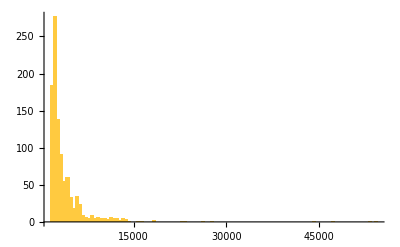

[総被引用数のZipf式へFit]

係数aは0.5であり、どちらかといえば低い値である。（学術出版にかかる引用では1を超えることが多い）被引用数が多いものを抽出しているためと考えられる。

[出版年のヒストグラム]

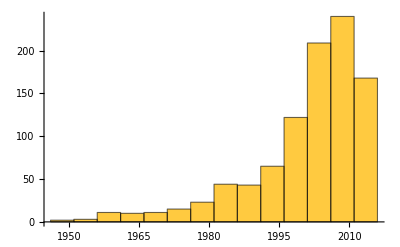

2005-2010年（10-15年前）の出版が多い。

[経過年と総被引用数との相関]

1次式に回帰させた場合、相関係数は0.13であり経過年だけでは被引用数をほとんど説明できない。

#### 順位変動

[順位相関]

年ごとの順位の入れ替わりを確認するために、Kendallの順位相関を求めた。相関は高く0.7から1の範囲で変動している。データ取得開始直後は同順位が多いため変動が激しいが、年を追うごとに相関は下がる傾向があるように推察される。出版が近年のものほど出版直後から引用されることが影響していると考えられる。

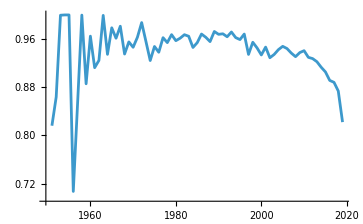

#### オブソレッセンス

1000件の論文につき、オブソレッセンス状態に達しているかを判定した。判定条件は下図の通りである。